# Checks for SQ Helix Structure different Dimers OD & CD

```mathematica
<<ModList.m
<<StylePlot.m
```

## Linear CD & OD Spectra

```mathematica
SetDirectory[NotebookDirectory[]]

OD12=Import["CD_OD_Test_12.out","Table"];
OD12=Take2[OD12,1,3];

CD12=Import["CD_OD_Test_12.out","Table"];
CD12=Take2[CD12,1,2];

OD23=Import["CD_OD_Test_23.out","Table"];
OD23=Take2[OD23,1,3];

CD23=Import["CD_OD_Test_23.out","Table"];
CD23=Take2[CD23,1,2];

OD34=Import["CD_OD_Test_34.out","Table"];
OD34=Take2[OD34,1,3];

CD34=Import["CD_OD_Test_34.out","Table"];
CD34=Take2[CD34,1,2];
```

/home/lindorfer/Post-Doc/TRCD/Spectra

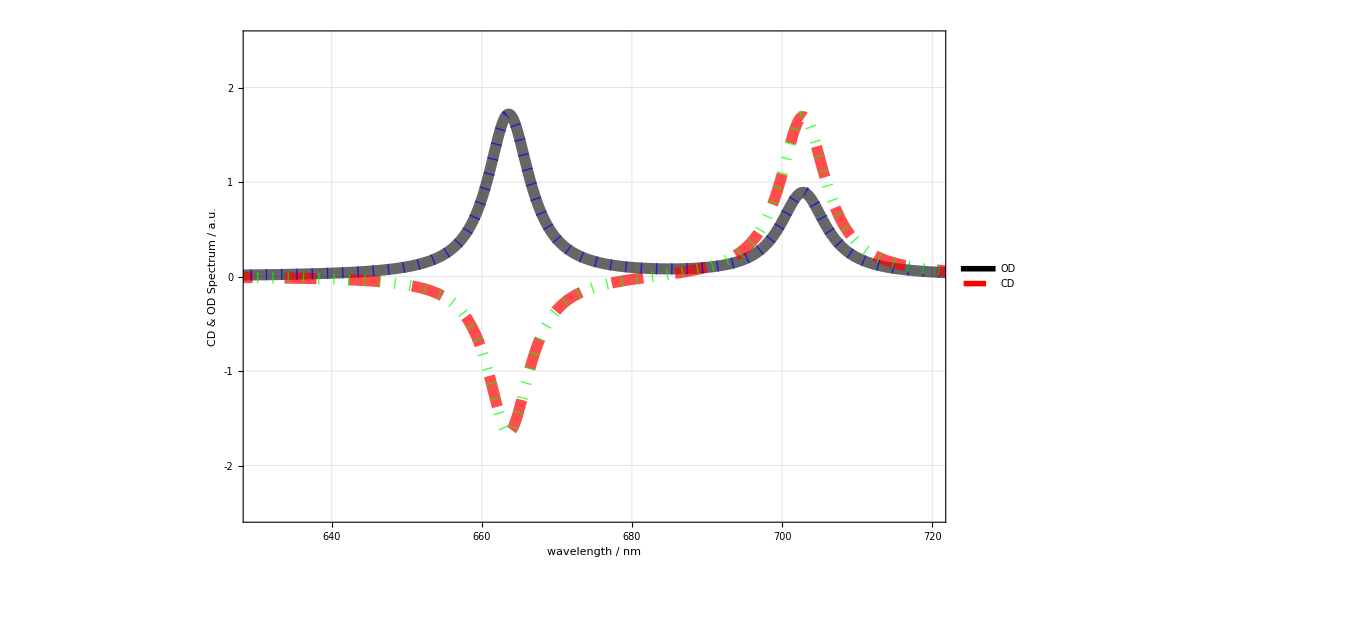

```mathematica
PlotLinSpec=StyleListPlot[{
ShiftX[ScaleY[OD12,1],0],ShiftX[ScaleY[CD12,2],0],
ShiftX[ScaleY[OD34,1],0],ShiftX[ScaleY[CD34,2],0]},

PlotStyle->{{Black,Thickness[0.008],Opacity[0.6]},{Red,Opacity[0.7],Dashing[0.023],Thickness[0.008]},{Blue,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]},{Green,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]}},
PlotRange->{{630,720},{-2.5,2.5}},
FrameLabels->{{"CD & OD Spectrum / a.u.",""},{"wavelength / nm",""}},
LegendText->Map[Style[#,{Bold,FontFamily->"Helvetica"}]&,{"OD","CD"}],
LegendPlacement->{{0.15,0.25}},
PlotLegendsLineColor->{Directive[Black,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5],Dashing[0.028]],Directive[Blue,AbsoluteThickness[5]],Directive[Green,AbsoluteThickness[5],Dashing[0.028]]},
GridLinesStyle->Directive[Gray, Dashed],
LegendSpacing->{0.1,-1.2},
ImageSize->1000
]
```

# Export

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lindorfer/Post-Doc/TRCD/Spectra